```mathematica
$HistoryLength=0;ClearAll["Global`*"]; 
SetDirectory["/home/dan/ResearchLocal/adiabatic/"];
```

```mathematica
fontweight="Bold"; fontsize=12;
```

## Strong Scaling (constant total domain size)

```mathematica
openMpiSS={{1,132275.8/176493.5},{2,123102.1/176493.5},{16,77893.9375/176493.5},{128,48100.11719/176493.5}};
intelSS={{1,176493.5/176493.5},{2,186225.1/176493.5},{16,112191.4375/176493.5},{128,66466.21875/176493.5},{1024,2929.36/176493.5}};
```

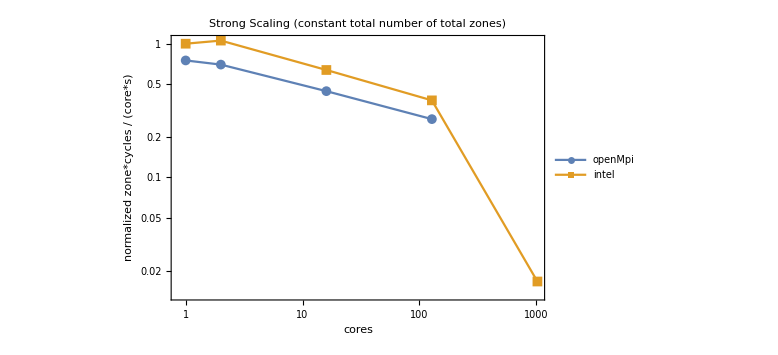

```mathematica
ssPlot=ListLogLogPlot[{openMpiSS,intelSS},PlotLabel->"Strong Scaling (constant total number of total zones)",PlotLegends->{"openMpi","intel"},FrameLabel->{"cores","normalized zone*cycles / (core*s)"},Frame->True,BaseStyle->{FontWeight->fontweight,FontSize->fontsize},PlotMarkers->{Automatic,10},Joined->True,ImageSize->Large]
```

```mathematica
Export["ssPlot.png",ssPlot]
```

ssPlot.png

## Weak Scaling v1 (constant number of zones per core)

```mathematica
openMpiWS={{2,105521.85/142544.6},{16,78211.75/142544.6},{128,75026.53125/142544.6}};
intelWS={{2,142544.6/142544.6},{16,113670.3125/142544.6},{128,85421.875/142544.6},{1024,28731/142544.6}};
```

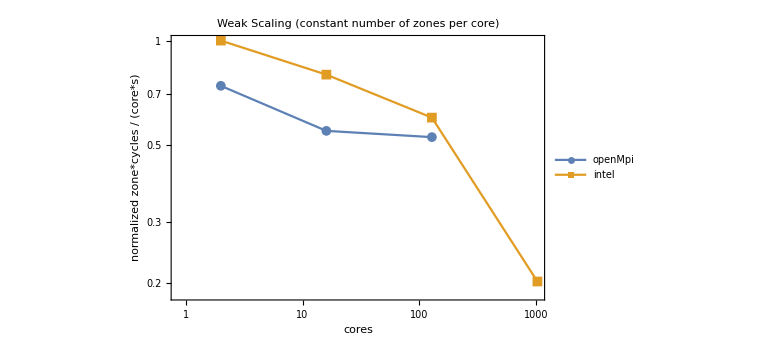

```mathematica
wsPlot=ListLogLogPlot[{openMpiWS,intelWS},PlotLabel->"Weak Scaling (constant number of zones per core)",PlotLegends->{"openMpi","intel"},FrameLabel->{"cores","normalized zone*cycles / (core*s)"},Frame->True,BaseStyle->{FontWeight->fontweight,FontSize->fontsize},PlotMarkers->{Automatic,10},Joined->True,ImageSize->Large]
```

```mathematica
Export["wsPlot1.png",wsPlot]
```

wsPlot1.png